# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can reproduce the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

## Recurrence

Fold this recurrence over Ζ and A:

ξ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ξ)
Λ←(Λ+aᵀ·a)

where

ξ is the current estimate of Ξ

a and ζ are matched rows of A and Ζ

Λ accumulates Aᵀ·A.

## Regularization By A-Priori

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, starting in section 1.1. The higher the order of the polynomial, the more MLE over-fits. Bishop presents MAP regularization as a cure for this over-fitting. RLS and KAL already regularize, by construction. In this section, we relate their regularization to MAP’s.

RLS and KAL each require an a-priori estimate of the unknown parameters and an a-priori uncertainty of that estimate to bootstrap recurrences. RLS takes the uncertainty as an information matrix. KAL takes the uncertainty as a covariance matrix. KAL additionally requires an estimate of observation noise, which arises in real problems and can often be estimated out-of-band. We show that RLS can and should be renormalized with observation noise to produce results equivalent to KAL and MAP.

Reproducing Bishop’s Example

### Bishop’s Training Set

First, create a sequence of Ν=10 inputs for a training set, equally spaced in [0..1].

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

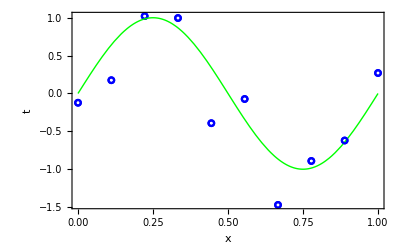

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

### Partials: Gradients of the Unknown Parameters

Write a function for partials.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
```

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
Manipulate[Module[{x},
With[{σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
<|"σζ2"->σζ2,"σξ2"-> σξ2,"rrls⟦1⟧"->MatrixForm[rrls⟦1⟧]|>
]]],
Column[{
Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

```mathematica
Manipulate[Module[{x},
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,
ts=bts⟦2⟧,
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{rrlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[rrlsFn,{x,0,1},PlotStyle->{Purple}]];Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]],
Column[{
Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

## Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

```mathematica
ClearAll[σ0,P,P0,ξ0,ξ0s,importanceFunction];
ClearAll[Ns,σ0,σ,ξ,importanceFunctions,ξs,Μ,ws];

Ns=1000;

Μ=9;

σ0=10.^6;
σ[0]=List/@ConstantArray[σ0,Μ+1];

ξ[0]=List/@ConstantArray[0.,Μ+1];

importanceFunctions[t_]:=
Table[
NormalDistribution[ξ[t]⟦i,1⟧,σ[t]⟦i,1⟧],
{i,Μ+1}];

ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[importanceFunctions[0]⟦i⟧],
{i,Μ+1},{j,Ns}];

Print[<|"σ"->σ,"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>];

ws[0]=ConstantArray[1./Ns,Ns];
Plus@@ws[0]
```

<|σ→σ,Dimensions[ξs[0]]→{10,1000}|>

1.

### Check Covariance

```mathematica
With[{μ=Mean/@ξs[0]},μ]
```

{-43757.4,101982.,29871.1,18382.,28295.8,-21093.3,-26256.7,28370.,16964.4,-17982.7}

```mathematica
With[{μ=Mean/@ξs[0]},
With[{r=ξs[0]⟦All,All⟧-μ},
Sqrt[Diagonal[r.rᵀ]/(Ns-1)]]]
```

{978039.,999398.,1.00674×10^6,1.01586×10^6,1.00226×10^6,1.02767×10^6,978377.,973858.,1.01668×10^6,1.0007×10^6}

```mathematica
StandardDeviation/@ξs[0]
```

{978039.,999398.,1.00674×10^6,1.01586×10^6,1.00226×10^6,1.02767×10^6,978377.,973858.,1.01668×10^6,1.0007×10^6}

### 3D Point Clouds

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

### Inspect the Initial Particles

Get a columns of ξs[0]:

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
ξcol[0,41]//MatrixForm
```

(-1.28101×10^6
-376416.
457910.
-1.20009×10^6
754805.
-26136.9
-1.61646×10^6
559732.
-646038.
-1.20733×10^6)

```mathematica
Manipulate[
partialsFn[m,bts⟦1⟧]//MatrixForm,
{{m,1},0,Μ+1,1,Appearance->{"Open","Labeled"}}]
```

```mathematica
partialsFn[Μ,bts⟦1⟧].ξcol[0,1]
```

{{69175.3},{-39846.3},{-171794.},{-322929.},{-493300.},{-685883.},{-902942.},{-1.13627×10^6},{-1.34556×10^6},{-1.41612×10^6}}

### Observations and Residuals

Observations are constant with time, but we include a time parameter just for fun. The particle cloud changes with time.

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

```mathematica
ClearAll[residuals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];
```

### Sum of Squared Residuals (SSR)

```mathematica
ClearAll[ssr];
ssr[t_,n_/;1≤n≤Ns]:=(residuals[t,n]ᵀ.residuals[t,n])⟦1,1⟧;
```

```mathematica
ClearAll[ssrs];
(ssrs=ssr[0,#]&/@Range[Ns])//Short
```

{6.77628×10^12,5.61854×10^13,«997»,2.83789×10^12}

### New Weights

Larger SSR means further from the observations. Let weights be inversely proportional to SSR, with divide-by-zero intentionally faulting because a zero SSR would signal an extremely improbable situation, most likely a bug somewhere else in the software.

```mathematica
(ws[1]= 1/ssrs/Plus@@(1/ssrs))//Short[#,3]&
```

{0.000759718,0.0000916265,0.000763916,0.000158675,«992»,0.000212251,0.000202435,0.000560576,0.00181405}

Check:

```mathematica
Plus@@ws[1]
```

1.

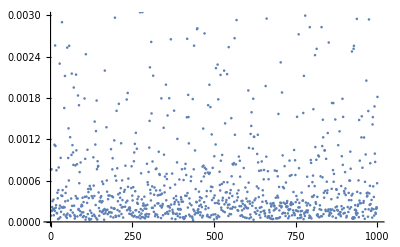

```mathematica
ListPlot[ws[1]]
```

### Cull the Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights];
(indexedWeights=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,0.000759718},«998»,{1000,0.00181405}}

Keep the top (p=25)%. In general, p should be the reciprocal of an integer that divides N_s because we are going to copy each survivor 1/p times to make a new sample of size N_s.

```mathematica
ClearAll[p,sortedIndexedWeights,topPWeights,topPIndexedWeights,topPIndices,topPParticles];
p=0.25;
<|"sortedIndexedWeights"->((sortedIndexedWeights=Reverse@SortBy[indexedWeights,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights=sortedIndexedWeights⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights=Last/@topPIndexedWeights)//Short),
"topPIndices"->((topPIndices=First/@topPIndexedWeights)//Short),
"topPParticles//Dims"->((topPParticles=(ξs[0]⟦All,#⟧&/@topPIndices)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{953,0.0474274},«998»,{436,0.0000255918}},topPIndexedWeights→{{953,0.0474274},«248»,{557,0.000839298}},topPWeights→{0.0474274,0.0270084,«247»,0.000839298},topPIndices→{953,715,203,232,679,965,780,904,370,178,«230»,993,387,635,92,797,561,978,295,413,557},topPParticles//Dims→{10,250},top 3 Particles→(-33960.3 | 157912. | 130920.
124153. | -820155. | 23689.5
-800458. | 1.28707×10^6 | 1.05856×10^6
962646. | 303775. | -1.82806×10^6
-302311. | -579469. | 458330.
-973982. | -714333. | -578074.
1.61409×10^6 | 986838. | -479233.
-1.04135×10^6 | 356299. | 147728.
266600. | -400093. | -202730.
445482. | -889310. | 1.17279×10^6)|>

Structure emerges after culling.

```mathematica
threeDPointClouds[topPParticles,σ0]
```

### Means of Top p Particles

```mathematica
ClearAll[μσ,μξ];
μξ[1]=Mean/@topPParticles
```

{41850.5,50053.4,497.987,-3243.56,-55051.3,-70581.9,43317.9,29724.1,-78021.8,-28273.1}

### Standard Deviations of Top p Particles

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles
```

{506460.,866323.,937747.,958363.,933551.,985112.,949986.,970278.,965778.,942770.}

Replace each particle with four (1/p) copies, each perturbed by this new σ_1. There are other ways to compute an importance sample of the top p particles. One way, possibly biased, is to keep the original survivor and add three perturbed copies. We first perform this latter sample (original joined to three copies) to check matrix dimensions, but proceed with the former sample (four copies).

#### Check Matrix Dimensions

Exhibit an example:

```mathematica
topPParticles⟦All,41⟧//MatrixForm
```

(288827.
-1.1817×10^6
95387.6
-1.28398×10^6
932990.
468962.
1.29065×10^6
-561674.
127033.
-310459.)

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

Check that the original appears in the first column.

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]-1},
conjColumns[
List/@ξ,
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(288827. | 753309. | 287618. | -172754.
-1.1817×10^6 | -2.46204×10^6 | -1.39048×10^6 | -711404.
95387.6 | 307465. | 1.02303×10^6 | 1.53593×10^6
-1.28398×10^6 | -2.80655×10^6 | -1.73909×10^6 | -1.42295×10^6
932990. | -906754. | 40043.1 | 1.54997×10^6
468962. | 3.30461×10^6 | 734579. | 775955.
1.29065×10^6 | 2.35515×10^6 | -463226. | 866109.
-561674. | 4783.31 | -1.5606×10^6 | -671454.
127033. | 110070. | -1.23536×10^6 | 570435.
-310459. | 1.51279×10^6 | -976482. | 1.23826×10^6)

#### Unbiased? Importance Sample

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]},
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(717307. | 425607. | 217061. | 97571.6
-1.6621×10^6 | 542053. | -1.42414×10^6 | -770225.
-1.06634×10^6 | -983878. | -1.14528×10^6 | 80772.6
-772667. | -1.02754×10^6 | -1.57402×10^6 | -2.44581×10^6
-37700.4 | 2.14021×10^6 | 1.11831×10^6 | 366981.
-189345. | 1.11937×10^6 | 1.07262×10^6 | 254090.
3.47693×10^6 | 3.01148×10^6 | 1.83537×10^6 | 556037.
-976063. | -1.29503×10^6 | -327839. | -1.64429×10^6
407733. | -775770. | 925148. | -2.23386×10^6
309434. | -740413. | -663079. | 138098.)

### A New Particle Cloud

```mathematica
topPParticles//Dimensions
```

{10,250}

```mathematica
(ξs[1]=Fold[conjColumns,make1OverP[#,σξ[1],p]&/@(topPParticlesᵀ)])//Dimensions
```

{10,1000}

```mathematica
threeDPointClouds[ξs[1],σ0]
```

### Package and Iterate

Abstract the procedure witnessed above and iterate.

We have some global variables, namely Μ and N_s. Assert, at the beginnings of all functions, that input dimensions match expectations w.r.t. these globals.

```mathematica
ClearAll[ssrFn,scalar,weights,cull,iterate];
On[Assert];
scalar[m_]:=(
Assert[{1,1}===Dimensions[m]];
m⟦1,1⟧);
ssrFn[A_,ζ_]:=
Function[ξ,
With[{ress=ζ-A.ξ},
With[{ssr=ressᵀ.ress},
ssr]]];
weights[xs_,ζ_][ξs_]:=
With[{A=partialsFn[Μ,xs]},
(Assert[Μ+1===Length[xs]];
Assert[Μ+1===Length[ζ]];
Assert[{Μ+1,Ns}===Dimensions[ξs]];
With[{ssrs=scalar/@ssrFn[A,ζ]/@(ξsᵀ)},
With[{ws= 1/ssrs/Plus@@(1/ssrs)},
Assert[Ns===Length[ws]];
Assert[Round[Plus@@ws,10.^-6]===1.];
ws]])];
cull[xs_,ζ_][p_,ξs_]:=Module[{indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPWeights,topPIndices,topPParticles},
indexedWeights=Function[ws,MapThread[List,{Range[Ns],ws}]];
sortedIndexedWeights=Function[ws,Reverse@SortBy[indexedWeights[ws],Last]];
topPIndexedWeights=Function[ws,sortedIndexedWeights[ws]⟦;;Floor[p Ns]⟧];
topPIndices=Function[ws,First/@topPIndexedWeights[ws]];
topPParticles=Function[ws,
With[{result=(ξs⟦All,#⟧&/@topPIndices[ws])ᵀ},
Assert[{Μ+1,Floor[p Ns]}===Dimensions[result]];
result]];
topPParticles[weights[xs,ζ][ξs]]];
iterate[xs_,ζ_][p_,ξs_]:=
With[{culled=cull[xs,ζ][p,ξs]},
With[
{σξ=StandardDeviation/@culled},
With[{result=
Fold[conjColumns,
make1OverP[#,σξ,p]&/@(culledᵀ)]},
Assert[{Μ+1,Ns}===Dimensions[result]];
result]]];
iterate[bts⟦1⟧,List/@bts⟦2⟧][p,ξs[0]]//threeDPointClouds[#,σ0]&
```

```mathematica
Norm/@Transpose[Fold[
iterate[bts⟦1⟧,List/@bts⟦2⟧][p,#1]&,
ξs[0],Range[15]]]
```

{2.46377×10^8,2.1414×10^8,2.42377×10^8,1.78489×10^8,1.92494×10^8,2.42586×10^8,3.0249×10^8,3.89312×10^8,3.35745×10^8,2.10507×10^8,2.69251×10^8,1.39821×10^8,1.28601×10^8,1.43008×10^8,2.36132×10^8,1.77683×10^8,2.05689×10^8,2.08702×10^8,1.85506×10^8,2.231×10^8,2.77473×10^8,2.19853×10^8,2.73461×10^8,2.81603×10^8,3.00009×10^8,3.75929×10^8,3.5468×10^8,2.26044×10^8,2.07733×10^8,4.15686×10^8,3.34562×10^8,2.03968×10^8,2.27091×10^8,2.38111×10^8,2.28408×10^8,1.37184×10^8,2.98448×10^8,2.44874×10^8,3.74468×10^8,3.17307×10^8,2.01802×10^8,2.53344×10^8,1.27938×10^8,1.83914×10^8,2.02712×10^8,1.8752×10^8,2.18828×10^8,3.42633×10^8,1.99865×10^8,2.22969×10^8,2.18935×10^8,1.6064×10^8,3.08865×10^8,3.70831×10^8,2.93268×10^8,3.42764×10^8,2.28912×10^8,2.4115×10^8,2.94308×10^8,2.83776×10^8,1.8723×10^8,2.04527×10^8,2.50538×10^8,2.37246×10^8,2.44746×10^8,2.61165×10^8,2.20742×10^8,2.3012×10^8,3.1077×10^8,2.39046×10^8,2.75929×10^8,3.41735×10^8,3.58611×10^8,2.37055×10^8,2.98638×10^8,3.10699×10^8,1.94356×10^8,2.51179×10^8,2.07167×10^8,2.73609×10^8,2.42704×10^8,1.0564×10^8,2.83199×10^8,2.97724×10^8,1.17506×10^8,1.6323×10^8,2.45849×10^8,2.31494×10^8,2.97754×10^8,1.47477×10^8,1.59444×10^8,2.72697×10^8,1.56153×10^8,2.90151×10^8,2.8776×10^8,2.40755×10^8,2.05832×10^8,3.24059×10^8,1.65719×10^8,2.38458×10^8,3.385×10^8,2.47042×10^8,3.10496×10^8,3.21171×10^8,1.43836×10^8,1.59908×10^8,2.49495×10^8,1.84768×10^8,2.35804×10^8,3.24645×10^8,3.15246×10^8,2.13652×10^8,3.22551×10^8,3.06432×10^8,2.60248×10^8,1.72419×10^8,2.61274×10^8,2.77068×10^8,1.51407×10^8,2.85334×10^8,2.83253×10^8,2.45624×10^8,3.67787×10^8,2.8116×10^8,1.97858×10^8,1.53477×10^8,2.0481×10^8,2.04593×10^8,2.66545×10^8,3.05877×10^8,1.87477×10^8,1.83991×10^8,3.07006×10^8,3.96718×10^8,2.05062×10^8,2.53353×10^8,2.00525×10^8,1.72653×10^8,1.89471×10^8,2.99136×10^8,3.13826×10^8,2.62386×10^8,2.81229×10^8,3.19392×10^8,2.99259×10^8,2.51607×10^8,2.54416×10^8,3.68911×10^8,2.41629×10^8,1.89818×10^8,1.40851×10^8,2.28699×10^8,2.44289×10^8,1.89661×10^8,3.022×10^8,2.12909×10^8,2.59835×10^8,2.44137×10^8,2.98261×10^8,2.9644×10^8,2.71733×10^8,2.83411×10^8,2.04223×10^8,3.05493×10^8,1.63548×10^8,2.38042×10^8,2.48938×10^8,2.69469×10^8,4.04905×10^8,3.13598×10^8,3.43764×10^8,2.87413×10^8,1.92539×10^8,2.93774×10^8,3.32005×10^8,2.94901×10^8,2.10958×10^8,2.49582×10^8,2.79218×10^8,2.09343×10^8,1.88414×10^8,1.29326×10^8,2.18134×10^8,1.90059×10^8,2.98928×10^8,2.31432×10^8,3.63978×10^8,2.42352×10^8,2.44065×10^8,3.85593×10^8,2.35357×10^8,2.79098×10^8,2.67075×10^8,2.50362×10^8,1.54253×10^8,1.98196×10^8,2.95227×10^8,1.29014×10^8,3.12829×10^8,1.90214×10^8,3.37842×10^8,1.67211×10^8,1.35393×10^8,2.51092×10^8,1.81714×10^8,1.81298×10^8,2.97239×10^8,1.86381×10^8,3.46091×10^8,2.09198×10^8,2.99472×10^8,1.95742×10^8,2.62809×10^8,3.1199×10^8,3.1224×10^8,2.43948×10^8,2.10264×10^8,3.128×10^8,3.37834×10^8,3.36953×10^8,2.71454×10^8,3.34991×10^8,3.93175×10^8,2.3585×10^8,2.73075×10^8,2.41092×10^8,3.35063×10^8,2.55082×10^8,1.86732×10^8,2.22166×10^8,2.34846×10^8,2.15218×10^8,2.1386×10^8,2.14926×10^8,2.17592×10^8,3.18844×10^8,3.32986×10^8,3.01588×10^8,3.00678×10^8,2.03416×10^8,3.02653×10^8,3.21452×10^8,2.3209×10^8,2.27051×10^8,3.2413×10^8,2.34694×10^8,2.5811×10^8,2.38659×10^8,2.99215×10^8,2.5746×10^8,3.2999×10^8,2.41614×10^8,2.3706×10^8,2.83798×10^8,3.30313×10^8,3.87487×10^8,2.26245×10^8,2.35441×10^8,1.39315×10^8,2.71418×10^8,2.38162×10^8,2.31233×10^8,3.07613×10^8,2.72882×10^8,4.10494×10^8,2.75888×10^8,2.16814×10^8,2.62144×10^8,3.28499×10^8,2.97113×10^8,2.96442×10^8,2.99892×10^8,4.35055×10^8,3.48633×10^8,2.70537×10^8,2.01429×10^8,3.17502×10^8,1.2097×10^8,2.2324×10^8,2.69106×10^8,2.62331×10^8,1.82901×10^8,2.3459×10^8,2.04695×10^8,2.32911×10^8,1.89136×10^8,2.63648×10^8,2.14832×10^8,2.2216×10^8,2.3541×10^8,3.24513×10^8,1.93392×10^8,2.62581×10^8,1.55954×10^8,1.98584×10^8,2.0103×10^8,1.49271×10^8,1.93349×10^8,2.54974×10^8,2.26371×10^8,2.9923×10^8,2.28469×10^8,2.79512×10^8,2.8787×10^8,2.12021×10^8,2.54979×10^8,2.56313×10^8,2.45437×10^8,3.78005×10^8,3.69358×10^8,2.78473×10^8,3.17934×10^8,2.24887×10^8,3.18197×10^8,1.80486×10^8,2.83669×10^8,2.92129×10^8,2.33486×10^8,3.33839×10^8,2.38846×10^8,3.23146×10^8,2.47981×10^8,3.59433×10^8,2.50549×10^8,2.39715×10^8,2.23976×10^8,2.87943×10^8,2.88643×10^8,2.53635×10^8,1.32591×10^8,2.1408×10^8,2.54676×10^8,2.557×10^8,2.67191×10^8,1.90687×10^8,1.90222×10^8,1.97252×10^8,3.59541×10^8,2.42907×10^8,3.41491×10^8,2.7047×10^8,2.19592×10^8,2.86028×10^8,2.55687×10^8,2.15735×10^8,1.4355×10^8,1.58735×10^8,1.54303×10^8,3.39656×10^8,2.61553×10^8,4.26531×10^8,1.74936×10^8,3.31466×10^8,2.73988×10^8,2.239×10^8,2.04256×10^8,1.53131×10^8,2.76189×10^8,1.94564×10^8,2.74218×10^8,1.50541×10^8,2.02999×10^8,1.75879×10^8,1.82487×10^8,2.17537×10^8,2.61876×10^8,2.12612×10^8,3.01205×10^8,1.60213×10^8,3.48673×10^8,2.87421×10^8,2.88508×10^8,3.109×10^8,1.9339×10^8,2.97449×10^8,2.41988×10^8,2.80719×10^8,2.12506×10^8,2.56396×10^8,2.58363×10^8,3.09464×10^8,2.57364×10^8,2.66679×10^8,1.96224×10^8,3.2525×10^8,2.63689×10^8,2.88001×10^8,3.17102×10^8,2.81822×10^8,2.70649×10^8,2.91346×10^8,2.46582×10^8,2.39829×10^8,2.62863×10^8,2.57869×10^8,2.30033×10^8,2.47966×10^8,2.6484×10^8,3.51214×10^8,2.77478×10^8,2.68319×10^8,1.88016×10^8,2.75227×10^8,1.92123×10^8,1.48138×10^8,2.06502×10^8,3.44709×10^8,2.10959×10^8,3.69943×10^8,2.98429×10^8,3.31052×10^8,2.88967×10^8,2.75046×10^8,2.64718×10^8,2.99139×10^8,2.72937×10^8,2.01971×10^8,2.44608×10^8,2.42887×10^8,4.17601×10^8,3.56485×10^8,2.76889×10^8,2.42097×10^8,3.01456×10^8,3.44544×10^8,2.80707×10^8,3.04943×10^8,3.73521×10^8,2.89066×10^8,2.80395×10^8,2.99751×10^8,2.85922×10^8,2.26609×10^8,2.58288×10^8,3.85723×10^8,3.57131×10^8,2.65245×10^8,2.15178×10^8,1.88332×10^8,2.32443×10^8,2.786×10^8,2.25881×10^8,2.23448×10^8,1.76548×10^8,3.3814×10^8,1.74145×10^8,2.62827×10^8,1.64731×10^8,1.81196×10^8,1.48605×10^8,3.58488×10^8,2.85604×10^8,2.13909×10^8,3.54353×10^8,3.66177×10^8,2.49142×10^8,1.58091×10^8,2.28302×10^8,2.80002×10^8,1.55993×10^8,2.22654×10^8,2.65936×10^8,2.21753×10^8,1.91953×10^8,1.78467×10^8,1.61553×10^8,1.22753×10^8,2.24694×10^8,3.5766×10^8,3.10626×10^8,2.09842×10^8,2.83652×10^8,2.09853×10^8,3.64428×10^8,2.21593×10^8,2.37646×10^8,2.13784×10^8,1.75935×10^8,2.82311×10^8,3.89307×10^8,2.76439×10^8,3.00714×10^8,2.47459×10^8,2.07376×10^8,2.98907×10^8,3.1585×10^8,4.09156×10^8,3.42885×10^8,3.23386×10^8,1.61878×10^8,2.53813×10^8,1.94742×10^8,2.29513×10^8,2.00889×10^8,2.41185×10^8,2.13952×10^8,1.94786×10^8,2.91304×10^8,3.01192×10^8,3.68605×10^8,2.17457×10^8,2.95548×10^8,3.04189×10^8,3.08586×10^8,2.09775×10^8,1.24006×10^8,1.68106×10^8,1.55354×10^8,2.91097×10^8,2.18426×10^8,1.51264×10^8,1.84275×10^8,3.10276×10^8,1.85924×10^8,3.74733×10^8,3.57379×10^8,2.66143×10^8,2.52683×10^8,3.02799×10^8,2.99167×10^8,2.1077×10^8,3.37715×10^8,2.08766×10^8,2.29332×10^8,3.19194×10^8,2.92001×10^8,3.36691×10^8,3.06943×10^8,3.26792×10^8,2.50124×10^8,2.75758×10^8,3.72233×10^8,2.90697×10^8,2.49869×10^8,3.65202×10^8,2.35007×10^8,2.41775×10^8,2.98277×10^8,2.36295×10^8,2.97834×10^8,2.5625×10^8,2.5644×10^8,1.25688×10^8,3.25518×10^8,2.12883×10^8,2.87476×10^8,1.21841×10^8,3.03328×10^8,3.89758×10^8,3.16962×10^8,3.15054×10^8,2.6725×10^8,2.14721×10^8,2.60346×10^8,3.22084×10^8,3.37624×10^8,2.73429×10^8,2.83832×10^8,3.13061×10^8,1.90256×10^8,2.01365×10^8,1.91248×10^8,2.5627×10^8,2.13164×10^8,3.49574×10^8,2.60169×10^8,3.42276×10^8,2.28697×10^8,3.97936×10^8,2.69936×10^8,2.19745×10^8,2.72366×10^8,2.79779×10^8,2.16617×10^8,2.28581×10^8,1.48573×10^8,2.28784×10^8,3.4737×10^8,2.66164×10^8,2.6516×10^8,2.65541×10^8,3.26675×10^8,2.12292×10^8,3.40515×10^8,2.22205×10^8,1.51244×10^8,2.60547×10^8,2.6463×10^8,2.62624×10^8,2.84415×10^8,2.74919×10^8,2.50529×10^8,1.87619×10^8,2.42189×10^8,2.53942×10^8,2.30797×10^8,2.03848×10^8,2.65368×10^8,2.63751×10^8,2.12226×10^8,2.90054×10^8,1.47255×10^8,1.8388×10^8,3.03464×10^8,3.10287×10^8,2.04903×10^8,2.90705×10^8,2.25866×10^8,2.4017×10^8,1.84832×10^8,2.15661×10^8,2.69097×10^8,3.41338×10^8,2.50019×10^8,4.12443×10^8,2.08503×10^8,2.94323×10^8,2.69591×10^8,3.0974×10^8,2.56397×10^8,2.67811×10^8,2.98734×10^8,2.2313×10^8,3.37939×10^8,2.61223×10^8,1.8829×10^8,3.05094×10^8,2.64712×10^8,3.97185×10^8,3.73216×10^8,3.53157×10^8,1.86046×10^8,2.81866×10^8,2.59874×10^8,2.15813×10^8,2.14304×10^8,3.36771×10^8,2.14554×10^8,2.24266×10^8,2.28708×10^8,1.56454×10^8,1.48849×10^8,2.08246×10^8,2.13358×10^8,3.08799×10^8,2.67713×10^8,3.36865×10^8,1.96582×10^8,2.66062×10^8,1.4958×10^8,1.95992×10^8,2.56151×10^8,3.16563×10^8,2.10903×10^8,1.19503×10^8,2.05986×10^8,2.87825×10^8,2.10122×10^8,2.40395×10^8,2.43429×10^8,2.62896×10^8,3.18721×10^8,2.41251×10^8,4.19951×10^8,2.98145×10^8,2.78386×10^8,2.70023×10^8,1.90089×10^8,3.31115×10^8,2.44648×10^8,2.39141×10^8,3.07092×10^8,2.89397×10^8,2.62879×10^8,1.01628×10^8,2.22914×10^8,2.44561×10^8,2.6047×10^8,1.88218×10^8,1.9113×10^8,2.8719×10^8,2.52604×10^8,1.82236×10^8,2.06621×10^8,1.73333×10^8,3.95935×10^8,2.19305×10^8,3.31432×10^8,2.36584×10^8,2.23036×10^8,9.91147×10^7,1.69543×10^8,1.74464×10^8,3.17161×10^8,3.17525×10^8,2.4209×10^8,1.5653×10^8,2.0775×10^8,2.00191×10^8,1.53419×10^8,2.47622×10^8,3.74819×10^8,2.84723×10^8,1.87918×10^8,1.9425×10^8,2.95616×10^8,2.91307×10^8,2.52668×10^8,3.30498×10^8,3.03552×10^8,3.64841×10^8,1.42317×10^8,3.44365×10^8,2.44478×10^8,2.98999×10^8,3.2479×10^8,2.16937×10^8,1.41731×10^8,1.51139×10^8,3.14707×10^8,2.99535×10^8,2.07112×10^8,2.06914×10^8,2.38931×10^8,3.15537×10^8,3.28855×10^8,2.99864×10^8,2.83149×10^8,3.9296×10^8,2.60317×10^8,2.77182×10^8,3.22336×10^8,2.60433×10^8,2.33638×10^8,2.81488×10^8,2.52045×10^8,1.36145×10^8,2.23959×10^8,1.59982×10^8,2.28141×10^8,1.50375×10^8,1.41101×10^8,1.69593×10^8,1.63037×10^8,3.55383×10^8,3.36434×10^8,2.68057×10^8,2.84014×10^8,3.36346×10^8,2.58935×10^8,2.65799×10^8,1.85899×10^8,2.17007×10^8,3.11536×10^8,1.26079×10^8,2.25909×10^8,3.09837×10^8,1.89691×10^8,2.79391×10^8,3.68171×10^8,2.91998×10^8,3.26034×10^8,3.17713×10^8,3.16339×10^8,3.2692×10^8,2.38208×10^8,2.80654×10^8,2.98071×10^8,1.98778×10^8,2.69675×10^8,2.65856×10^8,3.33353×10^8,2.41495×10^8,3.13578×10^8,3.83674×10^8,2.37634×10^8,2.64487×10^8,2.76053×10^8,2.16431×10^8,3.51147×10^8,1.46156×10^8,2.78802×10^8,1.88436×10^8,1.6361×10^8,2.56758×10^8,2.31726×10^8,2.29494×10^8,1.70236×10^8,2.20141×10^8,1.71443×10^8,2.10919×10^8,1.51957×10^8,3.10173×10^8,2.97949×10^8,3.49394×10^8,2.14935×10^8,2.45754×10^8,1.73012×10^8,1.64756×10^8,1.61234×10^8,2.24085×10^8,2.74714×10^8,2.30069×10^8,2.12223×10^8,1.55933×10^8,3.07452×10^8,1.37063×10^8,2.27344×10^8,1.18265×10^8,1.79053×10^8,2.96512×10^8,2.68974×10^8,2.77485×10^8,1.7211×10^8,3.29617×10^8,3.81363×10^8,1.89166×10^8,2.73977×10^8,1.74822×10^8,2.3375×10^8,1.78792×10^8,1.47159×10^8,2.32868×10^8,2.5503×10^8,2.90356×10^8,2.54604×10^8,2.88432×10^8,2.44396×10^8,3.15556×10^8,2.68251×10^8,2.5937×10^8,2.68516×10^8,2.74302×10^8,2.92607×10^8,2.92418×10^8,2.83621×10^8,2.66379×10^8,2.60025×10^8,1.96903×10^8,2.20224×10^8,1.78034×10^8,1.81222×10^8,3.51518×10^8,3.21423×10^8,2.37617×10^8,2.43873×10^8,2.85859×10^8,2.3402×10^8,2.71747×10^8,2.69202×10^8,2.72173×10^8,2.58847×10^8,1.92626×10^8,2.12445×10^8,1.81508×10^8,2.2995×10^8,3.16644×10^8,2.20713×10^8,2.55108×10^8,1.53249×10^8,2.32253×10^8,2.71656×10^8,3.09821×10^8,1.77446×10^8,3.18382×10^8,4.22624×10^8,2.42929×10^8,3.5158×10^8,3.74913×10^8,2.10174×10^8,2.67739×10^8,1.83019×10^8,2.76621×10^8,2.2898×10^8,1.38933×10^8,2.34054×10^8,1.30619×10^8,2.44667×10^8,3.76787×10^8,1.68353×10^8,2.51838×10^8,2.45272×10^8,3.06118×10^8,1.66391×10^8,2.55254×10^8,3.17147×10^8,2.43247×10^8,3.05965×10^8,1.93913×10^8,2.57136×10^8,1.9689×10^8,2.19821×10^8,3.36637×10^8,2.02525×10^8,2.30921×10^8,2.67326×10^8,1.68259×10^8,2.49583×10^8,2.13686×10^8,1.54677×10^8,3.4134×10^8,3.23231×10^8,3.47462×10^8,2.28997×10^8,2.96179×10^8,3.37895×10^8,2.35641×10^8,2.98855×10^8,2.29661×10^8,2.9406×10^8,3.08874×10^8,2.71465×10^8,1.36554×10^8,2.0677×10^8,2.49195×10^8,1.92356×10^8,1.70659×10^8,1.79968×10^8,3.36549×10^8,2.83922×10^8,2.72853×10^8,2.6339×10^8,3.24637×10^8,2.18851×10^8,1.91805×10^8,1.50994×10^8,2.11686×10^8,2.79908×10^8,2.10624×10^8,2.51228×10^8,1.85465×10^8,3.46978×10^8,2.96185×10^8,1.88632×10^8,2.31929×10^8,1.66171×10^8,2.34988×10^8,2.58792×10^8,2.50874×10^8,3.29139×10^8,2.3124×10^8,1.56746×10^8,2.43035×10^8,2.61134×10^8,2.26799×10^8,3.04815×10^8,2.99181×10^8,1.67698×10^8,2.46298×10^8,3.06222×10^8,2.56299×10^8,2.87093×10^8,2.9343×10^8,2.19129×10^8,2.2877×10^8,2.77872×10^8,3.1141×10^8,1.98545×10^8,2.63987×10^8,2.68649×10^8,1.95696×10^8,1.22637×10^8,2.46487×10^8,2.25424×10^8,3.53983×10^8,3.43403×10^8,3.36826×10^8,2.66665×10^8,1.90847×10^8,2.75256×10^8,3.8007×10^8,2.65012×10^8,3.92452×10^8,3.01639×10^8,2.77616×10^8,3.05774×10^8,3.01485×10^8,2.62935×10^8,3.30253×10^8,3.50489×10^8,4.28122×10^8,2.75558×10^8,4.28954×10^8,4.03596×10^8,1.76234×10^8,2.42523×10^8,2.52624×10^8,2.23742×10^8,1.99367×10^8,2.78218×10^8,3.34682×10^8,2.71314×10^8,3.0661×10^8,2.47269×10^8,2.93478×10^8,2.62242×10^8,2.41338×10^8,2.18287×10^8,3.5116×10^8,2.99785×10^8}

```mathematica
Fold[
iterate[bts⟦1⟧,List/@bts⟦2⟧][p,#1]&,
ξs[0],Range[15]]//
threeDPointClouds[#,σ0]&
```

## Conclusion

We have shown that Kalman folding (KAL) produces the same results as renormalized recurrent least squares (RLS) and maximum a-posteriori (MAP) for appropriate choices of covariances, i.e., regularization hyperparameters. We have further shown (numerically) that MAP produces the same results when its hyperparameters are swapped and inverted. 

KAL and RLS offer significant advantages in space-time efficiency by avoiding storage and multiplication of large matrices. In all cases, we avoid matrix inverses by solving linear systems internally.